```mathematica
numbers={a->1.,ν->0.07453,α->0.000002};
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

F:\Загрузки\Диплом\Diploma_Nb

```mathematica
SetOptions[{Plot,ListPlot,ListLinePlot,ListLogLinearPlot},PlotRange->Full,Axes->False,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],BaseStyle->{FontFamily->"Courier",FontSize->12, Bold},ImageSize->500,PlotStyle->{Red,PointSize[0.005]}];
```

```mathematica
NAFF[x_]:=Abs[Take[Table[Sum[x[[n]]*Exp[ⅈ*2π*β*n],{n,1,Length[x]}],{β,0,1,0.0001}],{1,5001}]]
```

```mathematica
NumPlace[x_]:=Position[NAFF[x],Max[NAFF[x]]][[1,1]]
```

```mathematica
FreqList[x_]:=Table[1.0*b/10000,{b,0,5000}]
```

```mathematica
Freq[x_]:=FreqList[x][[NumPlace[x]]]
```

```mathematica
TruePlot[x_]:=ListPlot[Transpose[{FreqList[x][[1;;5001]],NAFF[x][[1;;5001]]}],FrameLabel->{"ν","A, mm"}]
```

N = 128

```mathematica
sig100=Table[a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,128}];
```

0.0744

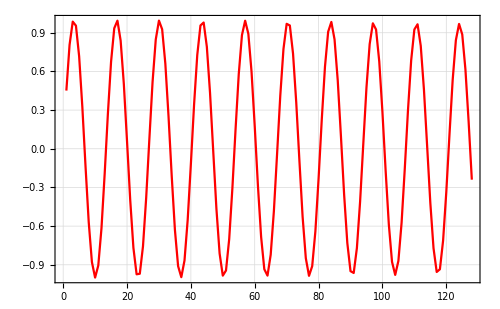

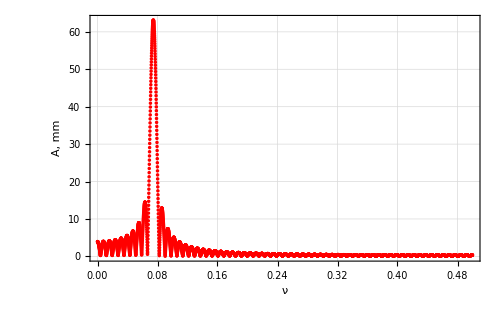

NAFF100.png

```mathematica
Freq100 =Freq[sig100]
Image100=ListLinePlot[sig100]
NAFF100=TruePlot[sig100]
Export["NAFF100.png",NAFF100]
```

N = 256

```mathematica
sig500=Table[a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,256}];
```

0.0745

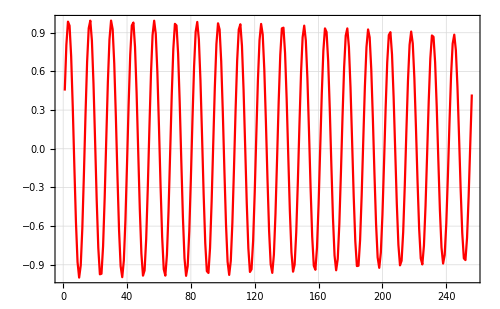

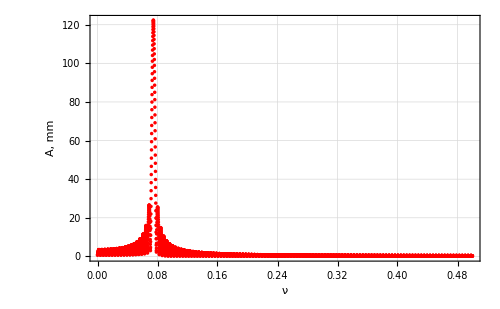

```mathematica
Freq500 =Freq[sig500]
Image500=ListLinePlot[sig500]
NAFF500=TruePlot[sig500]
```

N = 512

0.0745

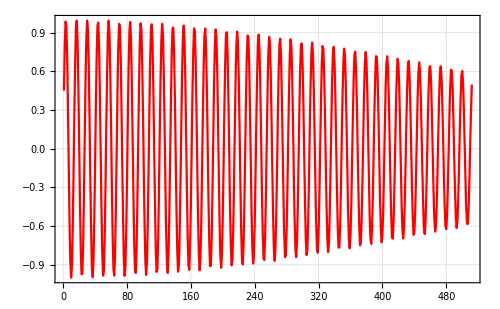

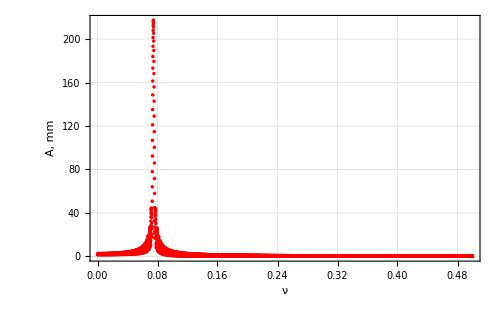

```mathematica
sig1000=Table[a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,512}];
Freq1000 =Freq[sig1000]
Image1000=ListLinePlot[sig1000]
NAFF1000=TruePlot[sig1000]
```

N = 1024

0.0745

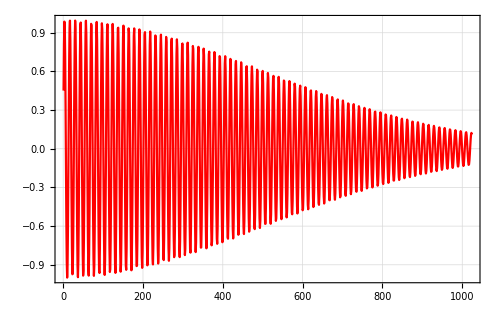

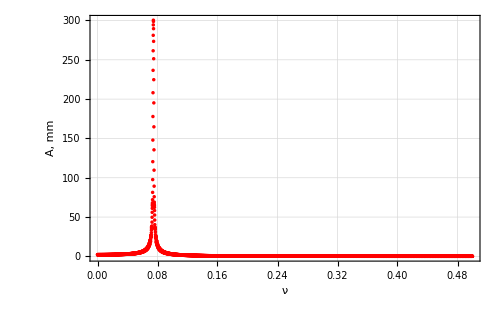

```mathematica
sig1500=Table[a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,1024}];
Freq1500 =Freq[sig1500]
Image1500=ListLinePlot[sig1500]
NAFF1500=TruePlot[sig1500]
```

N = 4096

0.0745

-Graphics-

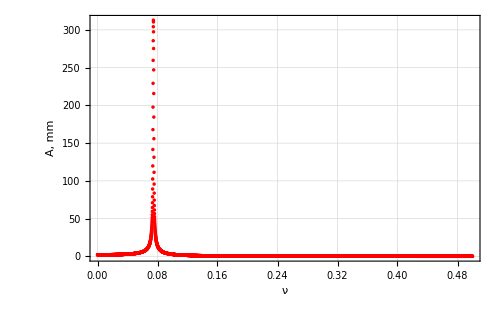

NAFF3000.png

```mathematica
sig3000=Table[a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,4096}];
Freq3000 =Freq[sig3000]
Image3000=ListLinePlot[sig1000]
NAFF3000=TruePlot[sig3000]
Export["NAFF3000.png",NAFF3000]
```

```mathematica
depen =Transpose[{{128,256,512,1024,4096},{Freq100, Freq500,Freq1000,Freq1500,Freq3000}*10^5-ν*10^5}/.numbers];
```

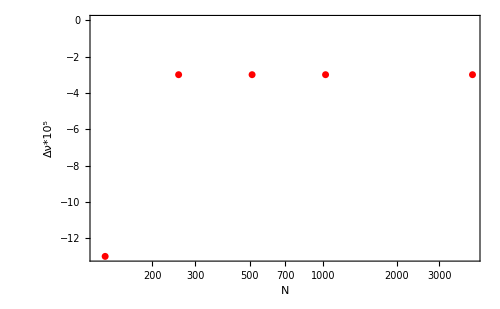

```mathematica
DeltaNAFF=ListLogLinearPlot[depen,Axes->True,FrameLabel->{"N","Δν*10^5"},PlotStyle->{Red,PointSize[0.01]}]
```

```mathematica
Export["DeltaNAFF.png",DeltaNAFF]
```

DeltaNAFF.png